```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[-1/z [t]Sqrt[(1-(1+zh^2μ^2)(z[t]/zh)^3+z[t]^4μ^2/zh^2)-z'[t]^2/(1-(1+zh^2μ^2)(z[t]/zh)^3+z[t]^4μ^2/zh^2)]+q μ (1-z[t]/zh),z[t],t]
```

-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0

```mathematica
zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs)/.{μ->1.635,zh->1,zs->0.1}
```

6.7842

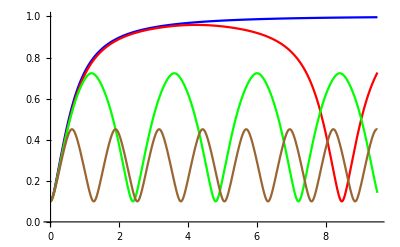

```mathematica
Block[
{A,B,C1},
B = {0,7,9,14};
C1={Blue,Red,Green,Brown,Magenta};
A=Table[Plot[Evaluate[z[t]/.NDSolve[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->1.635,zh->1,q->B[[i]]},z[0]==0.1,z'[0]==0},z,{t,0.01,9.5},Method->"ExplicitRungeKutta"
]],{t,0.01,9.5},PlotRange->{{0.01,9.5},{0,1}},PlotStyle->C1[[i]]],{i,1,4}];
Show[A]
]
```

```mathematica
zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs)/.{μ->1.3,zh->1,zs->0.1}
```

8.53623

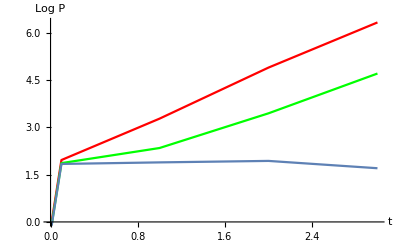

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{{0.01,Log[pz[0.01,0,1.3,1,0.1]]},{0.1,Log[pz[0.1,0,1.3,1,0.1]]},{1,Log[pz[1,0,1.3,1,0.1]]},{2,Log[pz[2,0,1.3,1,0.1]]},{3,Log[pz[3,0,1.3,1,0.1]]}},PlotStyle->Red],
ListLinePlot[{{0.01,Log[pz[0.01,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,0.8*qcrit[1.3,1,0.1],1.3,1,0.1]]}},PlotStyle->Green],
ListLinePlot[{{0.01,Log[pz[0.01,qcrit[1.3,1,0.1],1.3,1,0.1]]},{0.1,Log[pz[0.1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{1,Log[pz[1,qcrit[1.3,1,0.1],1.3,1,0.1]]},{2,Log[pz[2,qcrit[1.3,1,0.1],1.3,1,0.1]]},{3,Log[pz[3,qcrit[1.3,1,0.1],1.3,1,0.1]]}}]
,AxesLabel->{t,Log P}
]
]
```

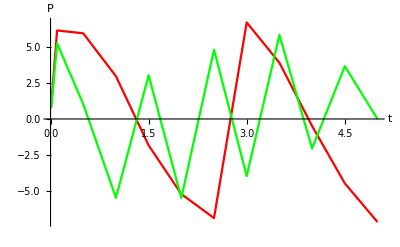

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{
{0.01,pz[0.01,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{0.1,pz[0.1,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{0.5,pz[0.5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{1,pz[1,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{1.5,pz[1.5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{2,pz[2,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{2.5,pz[2.5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{3,pz[3,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{3.5,pz[3.5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{4,pz[4,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{4.5,pz[4.5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]},
{5,pz[5,1.2qcrit[1.3,1,0.1],1.3,1,0.1]}
},
PlotStyle->Red],
ListLinePlot[{
{0.01,pz[0.01,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{0.1,pz[0.1,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{0.5,pz[0.5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{1,pz[1,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{1.5,pz[1.5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{2,pz[2,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{2.5,pz[2.5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{3,pz[3,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{3.5,pz[3.5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{4,pz[4,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{4.5,pz[4.5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]},
{5,pz[5,2.3qcrit[1.3,1,0.1],1.3,1,0.1]}
},
PlotStyle->Green],
AxesLabel->{t,P}
]
]
```

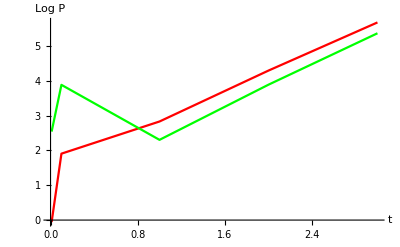

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A,z,pz1},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
pz1[t1_,q1_,μ1_,zh1_,zs1_]:=1/(D[fz[zh1,μ1,z],z]/.{z->zm[t1,q1,μ1,zh1,zs1]})1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{{0.01,Log[pz[0.01,4,1.3,1,0.1]]},{0.1,Log[pz[0.1,4,1.3,1,0.1]]},{1,Log[pz[1,4,1.3,1,0.1]]},{2,Log[pz[2,4,1.3,1,0.1]]},{3,Log[pz[3,4,1.3,1,0.1]]}},PlotStyle->Red],
ListLinePlot[{{0.01,Log[Abs[pz1[0.01,4,1.3,1,0.1]]]},{0.1,Log[Abs[pz1[0.1,4,1.3,1,0.1]]]},{1,Log[Abs[pz1[1,4,1.3,1,0.1]]]},{2,Log[Abs[pz1[2,4,1.3,1,0.1]]]},{3,Log[Abs[pz1[3,4,1.3,1,0.1]]]}},PlotStyle->Green]
,AxesLabel->{t,Log P},MaxRecursion->6
]
]
```

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A,z,pz1},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
pz1[t1_,q1_,μ1_,zh1_,zs1_]:=1/(D[fz[zh1,μ1,z],z]/.{z->zm[t1,q1,μ1,zh1,zs1]})1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[Table[pz1[i,4,1.3,1,0.1],{i,0.01,5,0.1}]]
]
```

{-12.6774+0. ⅈ,-46.3022+0. ⅈ,-25.181+0. ⅈ,-15.1805+0. ⅈ,-10.8154+0. ⅈ,-8.83487+0. ⅈ,-8.02516+0. ⅈ,-7.90148+0. ⅈ,-8.25832+0. ⅈ,-9.01063+0. ⅈ,-10.1315+0. ⅈ,-11.6256+0. ⅈ,-13.5167+0. ⅈ,-15.8417+0. ⅈ,-18.6482+0. ⅈ,-21.9939+0. ⅈ,-25.9431+0. ⅈ,-30.5745+0. ⅈ,-35.975+0. ⅈ,-42.2434+0. ⅈ,-49.4941+0. ⅈ,-57.8566+0. ⅈ,-67.4784+0. ⅈ,-78.5293+0. ⅈ,-91.1985+0. ⅈ,-105.709+0. ⅈ,-122.315+0. ⅈ,-141.291+0. ⅈ,-163.006+0. ⅈ,-187.73+0. ⅈ,-216.169+0. ⅈ,-248.316+0. ⅈ,-285.195+0. ⅈ,-327.509+0. ⅈ,-375.067+0. ⅈ,-429.842+0. ⅈ,-492.187+0. ⅈ,-563.076+0. ⅈ,-644.188+0. ⅈ,-736.456+0. ⅈ,-842.989+0. ⅈ,-950.811+0. ⅈ,-1071.21+0. ⅈ,-1229.52+0. ⅈ,-1403.1+0. ⅈ,-1609.57+0. ⅈ,-1833.4+0. ⅈ,-2105.76+0. ⅈ,-2310.05+0. ⅈ,-2579.71+0. ⅈ}

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A,z,pz1},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
pz1[t1_,q1_,μ1_,zh1_,zs1_]:=1/(D[fz[zh1,μ1,z],z]/.{z->zm[t1,q1,μ1,zh1,zs1]})1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[pz[0.01,4,1.3,1,0.1]];
Print[Abs[pz[0.01,4,1.3,1,0.1]]];
Print[pz1[0.01,4,1.3,1,0.1]];
Print[Abs[pz1[0.01,4,1.3,1,0.1]]];
]
```

0.945837+0. ⅈ

0.945837

-12.6774+0. ⅈ

12.6774

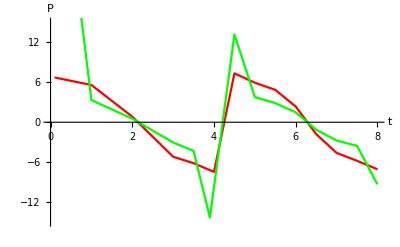

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A,z,pz1},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
pz1[t1_,q1_,μ1_,zh1_,zs1_]:=1/(D[fz[zh1,μ1,z],z]/.{z->zm[t1,q1,μ1,zh1,zs1]})1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Show[
ListLinePlot[{{0.1,pz[0.1,4,1.3,1,0.1]},{1,pz[1,9,1.3,1,0.1]},{2,pz[2,9,1.3,1,0.1]},{3,pz[3,9,1.3,1,0.1]},{3.5,pz[3.5,9,1.3,1,0.1]},{4,pz[4,9,1.3,1,0.1]},{4.5,pz[4.5,9,1.3,1,0.1]},{5,pz[5,9,1.3,1,0.1]},{5.5,pz[5.5,9,1.3,1,0.1]},{6,pz[6,9,1.3,1,0.1]},{6.5,pz[6.5,9,1.3,1,0.1]},{7,pz[7,9,1.3,1,0.1]},{7.5,pz[7.5,9,1.3,1,0.1]},{8,pz[8,9,1.3,1,0.1]}},PlotStyle->Red],
ListLinePlot[{{0.1,-pz1[0.1,4,1.3,1,0.1]},{1,-pz1[1,9,1.3,1,0.1]},{2,-pz1[2,9,1.3,1,0.1]},{3,-pz1[3,9,1.3,1,0.1]},{3.5,-pz1[3.5,9,1.3,1,0.1]},{3.9,-pz1[3.9,9,1.3,1,0.1]},{4.5,-pz1[4.5,9,1.3,1,0.1]},{5,-pz1[5,9,1.3,1,0.1]},{5.5,-pz1[5.5,9,1.3,1,0.1]},{6,-pz1[6,9,1.3,1,0.1]},{6.5,-pz1[6.5,9,1.3,1,0.1]},{7,-pz1[7,9,1.3,1,0.1]},{7.5,-pz1[7.5,9,1.3,1,0.1]},{8,-pz1[8,9,1.3,1,0.1]}},PlotStyle->Green]
,AxesLabel->{t, P},MaxRecursion->6,PlotRange->{{0,8},{-15,15}}
]
]
```